```mathematica
(* This notebook contains examples for the PET-functions
 -CalcThermoBaro-          calculate various geothermometers and geobarometers
Most examples are performed with mineral analyses from the file "gtb"
*)
(* This top-cell must be run once before any example can be performed.  *)

(* Define the directory,where the PET-files reside (e.g. C:\Eigene Dateien\Pet) and load PET. *)$PetDirectory="C:\Dokumente und Einstellungen\dachsedgar\Eigene Dateien\Pet\Pet7.0";

SetDirectory[$PetDirectory];
DeclarePackage["DEFDAT`",{"Dataset"}];
Dataset[Dataset-> B88];
```

```mathematica
(* Example 1: display the usage for the PET-function -CalcThermoBaro-  *) 
CalcThermoBaro::usage
```

CalcThermoBaro[{gtb1, gtb2, ...},"inputfile","outputfile"] 
calculates various geothermobarometers (gtb's).
Each gtb in the list {gtb1, gtb2, ...} has the form:
{gtb_specification,{min,max,step}}:
<gtb_specification> is either gt+number for the installed geothermometers (see the list below),
or gb+number for the geobarometers. gt1 e.g. represents the garnet-biotite thermometer (FunctionName: GT1).
{min, max, step} define the pressure range (in bar) and interval, for which temperatures are calculated
in the case of a geothermometer, and vice versa for geobarometers (T in C). 
Some gtb's require a third parameter after {min, max, step}, e.g. specifiying an Al2SiO5-polymorph).
"inputfile" must have been created earlier with 

CalcFormula["inputfile",CalcFormulaMode->Gtb]

(the option CalcFormulaMode->Gtb is required to calculate specific mineral-chemical
parameters e.g. for clinopyroxene and garnet in the grt-cpx thermometer, etc.).
If "inputfile" contains more than one pair of e.g. grt and bt, the analyses are grouped together
in order of their appearance, 1. grt with 1. bt, 2. grt with 2. bt, etc. The data are written to
"outputfile.ptx" for later use and are also returned to the screen and have the form:

1.element: specification of the gtb (e.g. gt1),
2.element: name of "inputfile",
3.element: lnKD for that geothermobarometer,
4.element: calibration that has been used
5.element: list of PT-data.

The user is responsible for not applying the various calibrations beyond the range of their
compositional applicability.

The following geothermometers (gt's) are available in PET:
speci-    explanation                               FunctionName
fication

gt1       garnet - biotite          FeMg-1          GT1
gt2       garnet - phengite         FeMg-1          GT2
gt3       garnet - chlorite         FeMg-1          GT3
gt4       biotite - chlorite        FeMg-1          GT4
gt5       phengite - biotite        FeMg-1          GT5
gt6       garnet - ilmenite         FeMn-1          GT6
gt7       garnet - clinopyroxene    FeMg-1          GT7
gt8       plagioclase - muscovite   NaK-1           GT8
gt9       garnet - orthopyroxene    FeMg-1          GT9
gt10      ortho-/clinopyoxene       CaMg-1          GT10
gt11      orthopyroxene - biotite   FeMg-1          GT11
gt12      garnet - olivine          FeMg-1          GT12
gt13      clinopyroxene - olivine   FeMg-1          GT13
gt14      garnet - hornblende       FeMg-1          GT14
gt15      garnet - cordierite       FeMg-1          GT15
gt16      garnet - staurolite       FeMg-1          GT16
gt17      garnet - chloritoid       FeMg-1          GT17
gt18      chlorite - chloritoid     FeMg-1          GT18
gt19      biotite - chloritoid      FeMg-1          GT19
gt20      garnet - spinel           FeMg-1          GT20
gt21      olivine - spinel          FeMg-1          GT21
gt22      cordierite - spinel       FeMg-1          GT22
gt23      amphibole - plagioclase   exchange        GT23
gt24      calcite - dolomite        solvus          GT24
gt25      plagioclase - Kfeldspar   solvus          GT25

The following geobarometers (gb's) are available in PET:
speci-    explanation                               FunctionName
fication

gb1       GASP                                      GB1
gb2       garnet-plagioclase-white mica-biotite     GB2
gb3       garnet-plagioclase-white mica             GB3
gb4       garnet-plagioclase-biotite                GB4
gb5       garnet-white mica-Al2SiO5-quartz          GB5
gb6       garnet-white mica-biotite-Al2SiO5-quartz  GB6
gb7       GRAIL                                     GB7
gb8       chlorite-biotite-white mica               GB8
gb9       garnet-amphibole-plagioclase              GB9
gb10      albite = jadeite + quartz                 GB10
gb11      garnet-phengite-omphacite                 GB11
gb12      amphibole - chlorite                      GB12
gb13      Al-in-hornblende                          GB13
gb14      Al-in-orthopyroxene                       GB14
gb15      garnet-orthopyroxene-plagioclase-quartz   GB15
gb16      garnet-clinopyroxene-plagioclase-quartz   GB16

For most gtb's there are several calibrations available. The program returns the latest version
by default, but the user can choose the calibration most appropriate for his/her purpose.
Type

FunctionName::usage (e.g. GT1::usage)

to see the available calibrations for each gtb (examples are also given for each gtb, using data from the file
"gtb.fu". This file is an arbitrary collection of analyses, so results are in no way meaningful !).

To change the default calibration use:

SetOptions[FunctionName, FunctionNameCalibration->YourChoice(Number: 0,1,2,etc.)];

before calling -CalcThermoBaro-.
(Number=0 is the default, otherwise number must be 1, 2, 3, etc., depending on how many calibrations there are).

Example: 

SetOptions[GT1,GT1Calibration->16];
result = CalcThermoBaro[{{gt1,{2000,6000,2000}},
{gb1,{400,600,25},sillimanite}},"gtb","test"]

This calculates the garnet-biotite thermometer and the GASP barometer from mineralchemical data of the file
"gtb.fu" (created with CalcFormula["gtb", CalcFormulaMode -> Gtb]), storing results in
the file "test.ptx", using the Hodges & Spear calibration for the garnet-biotite geothermometer.
ReturnValue:

{{{grt-bt FeMg-1}, {gtb, {lnKD = -2.08361, GT1Calibration = Hodges & Spear (1982), eq.(9)}},
{{472.31, 2000.}, {478.94, 4000.}, {485.56, 6000.}}},
{{GASP barometer}, {gtb, {lnK = -1.62754, GB1Calibration = Koziol (1989), sillimanite}},
{{400., 3142.22}, {425., 3681.78}, {450., 4221.1}, {475., 4760.2}, {500., 5299.06}, {525., 5837.68},
{550., 6376.07}, {575., 6914.23}, {600., 7452.15}}}}

Data can be plotted with PlotRea[result], and the intersection of grt/bt and GASP can be calculated with
CalcReaIntersection[result].
Package name: GTB.m
PET: Petrological Elementary Tools, (c) Edgar Dachs.

```mathematica
(* Example 2: display the available calibrations for the garnet-biotite geothermometer (GT1)  *) 
GT1::usage
```

Garnet - biotite FeMg-1 exchange geothermometer.

Option for selecting a specific calibration:
Name              Value        Reference

GT1Calibration -> 0 (default)  Holdaway (2000), Am Min 85:881-892
                  1            Gessmann et al. (1997), Am Min 82:1225-1240
                  2            Holdaway et al. (1997), Am Min 82:582-595
                  3            Kleemann & Reinhardt (1994), Eur J Mineral 6:925-941,
                               with Berman (1990) garnet model
                  4            Bhattacharya et al. (1992), Contrib Mineral Petrol 111:87-93,
                               with Ganguly & Saxena (1984) garnet model
                  5            Bhattacharya et al. (1992), Contrib Mineral Petrol 111:87-93,
                               with Hackler & Wood (1984) garnet model
                  6            Dasgupta et al. (1991), Contrib Mineral Petrol 109:130-137
                  7            Williams & Grambling (1990), Am Min 75:886-908
                  8            Aranovich et al. (1988), Geokhimiya 5:668-676
                  9            Hoinkes (1986), Contrib Mineral Petrol 92:393-399
                  10           Indares & Martignole (1985), Model B, Am Min 70:272-278
                  11           Indares & Martignole (1985), Model A, Am Min 70:272-278
                  12           Ganguly & Saxena (1984), asymmetric garnet model, Am Min 69:88-97
                  13           Ganguly & Saxena (1984), symmetric garnet model, Am Min 69:88-97
                  14           Perchuk & Lavrent'eva (1983), In: Saxena, SK ed., Kinetics and
                               Equilibrium in Mineral Reactions. Springer Verlag, pp.199-240
                  15           Pigage & Greenwood (1982), Am J Sci 282:943-969
                  16           Hodges & Spear (1982), Am Min 67:1118-1134
                  17           Lavrent'yeva & Perchuk (1981), Dokl Akad Nauk SSSR 260:731-734
                  18           Ferry & Spear (1978), Contrib Mineral Petrol 66:113-117
                  19           Holdaway & Lee (1977), Contrib Mineral Petrol 63:175-198
                  20           Goldman & Albee (1977), Am J Sci 277:750-767,
                               with 1000ln(alfa) according to Matthews et al. (1983)
                  21           Goldman & Albee (1977), Am J Sci 277:750-767,
                               with 1000ln(alfa) according to Bottinga & Javoy (1973)
                  22           Thompson (1976), Am J Sci 276:425-454

Example (using default calibration): 

result = CalcThermoBaro[{{gt1,{3000,6000,3000}}},"gtb","test"]

ReturnValue:
{{{grt-bt FeMg-1}, {gtb, {lnKD = -2.08361, GrtBtCalibration = Holdaway (2000)}},
{{559.52, 3000}, {567.22, 6000}}}}

Example (using calibration No. 18): 

SetOptions[GT1, GT1Calibration->18];
result = CalcThermoBaro[{{gt1,{3000,6000,3000}}},"gtb","test"]

ReturnValue:
{{{grt-bt FeMg-1}, {gtb, {lnKD = -2.08361, GT1Calibration = Ferry and Spear (1978), eq. (7)}},
{{465.91, 3000}, {475.92, 6000}}}}

Package name: GTB.m
PET: Petrological Elementary Tools, (c) Edgar Dachs.

```mathematica
(* Example 3: calculate the formulae for analyses in the file "gtb" (PET-function -CalcFormula-) and
then use the PET-function -CalcThermoBaro- to compute the garnet-biotite geothermometer (gt1) for pressures from 1 to 10 kb in 1kb-steps, saving data to the file "test" *) 

file = "gtb";
CalcFormula[file, CalcFormulaMode -> Gtb];
result=CalcThermoBaro[{{gt1,{1000,10000,1000}}},file,"test"]
```

Message from -CalcFormula-: creating file "gtb.fu".

{{{grt-bt FeMg-1},{gtb,{lnKD = -2.08361,GT1Calibration = Holdaway (2000)}},{{554.39,1000.},{556.95,2000.},{559.52,3000.},{562.09,4000.},{564.66,5000.},{567.22,6000.},{569.79,7000.},{572.36,8000.},{574.93,9000.},{577.49,10000.}}}}

```mathematica
(* Example 4: Use the PET-function -CalcThermoBaro- to compute the garnet-biotite geothermometer (gt1) for pressures from 1 to 10 kb in 1kb-steps, saving data to the file "test". *)
(* Change the default calibration to number 16, which is the Hodges & Spear (1982) calibration (see GT1::usage) *) 

SetOptions[GT1,GT1Calibration->22];
result=CalcThermoBaro[{{gt1,{1000,10000,1000}}},file,"test"]
```

{{{grt-bt FeMg-1},{gtb,{lnKD = -2.08361,GT1Calibration = Thompson (1976), Table 1}},{{485.17,1000.},{491.59,2000.},{498.01,3000.},{504.44,4000.},{510.86,5000.},{517.28,6000.},{523.7,7000.},{530.13,8000.},{536.55,9000.},{542.97,10000.}}}}

```mathematica
(* Example 5: Use the PET-function -CalcThermoBaro- to compute the garnet-biotite geothermometer (gt1) for pressures from 1 to 10 kb in 1kb-steps, and the GASP barometer (gb1), for temperatures between 400 and 700 C, in 50C-steps for the data file "hs78b". Save data to the file "test", plot the results and calculate the intersection *)

file = "hs78b";
CalcFormula[file,CalcFormulaMode->Gtb];
result=CalcThermoBaro[{{gt1,{1000,10000,1000}},{gb1,{400,700,50},kyanite}},file,"test"]
plot1=PlotRea[result];
CalcReaIntersection[result]
```

Message from -CalcFormula-: creating file "hs78b.fu".

{{{grt-bt FeMg-1},{hs78b,{lnKD = -2.08361,GT1Calibration = Thompson (1976), Table 1}},{{485.17,1000.},{491.59,2000.},{498.01,3000.},{504.44,4000.},{510.86,5000.},{517.28,6000.},{523.7,7000.},{530.13,8000.},{536.55,9000.},{542.97,10000.}}},{{GASP barometer},{hs78b,{lnK = -1.49787,GB1Calibration = Koziol (1989),kyanite}},{{400.,2928.19},{450.,3999.02},{500.,5069.85},{550.,6140.68},{600.,7211.52},{650.,8282.35},{700.,9353.18}}}}

{{5350.65,513.111,{1,2}}}

calculating PT data of the reaction:

{-3. an,1. gr,2. ky,1. qz}

calculating PT data of the reaction:

{-1. alm,-1. phl,1. ann,1. py}

{{{{-3. an,1. gr,2. ky,1. qz},{a(alm)=GrtBerman, a(phl)=BtMcMullin, a(ann)=BtMcMullin, a(py)=GrtBerman},{{328.543,1000.},{379.693,2000.},{430.72,3000.},{481.588,4000.},{532.26,5000.},{582.7,6000.},{632.876,7000.},{682.758,8000.},{732.322,9000.},{781.547,10000.}}},{{-1. alm,-1. phl,1. ann,1. py},{a(alm)=GrtBerman, a(phl)=BtMcMullin, a(ann)=BtMcMullin, a(py)=GrtBerman},{{464.944,1000.},{469.823,2000.},{474.684,3000.},{479.528,4000.},{484.353,5000.},{489.16,6000.},{493.95,7000.},{498.721,8000.},{503.475,9000.},{508.21,10000.}}}},{Dataset -> B88,SampleFile->hs78b}}

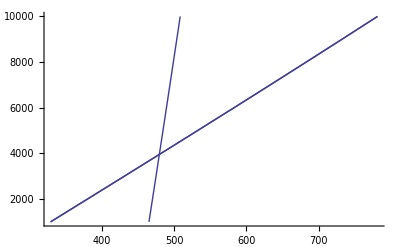

{{3955.16,479.311,{1,2}}}

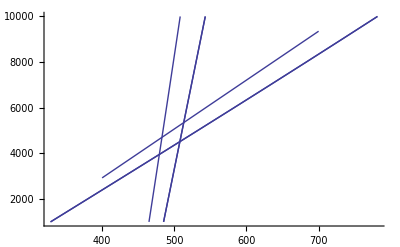

```mathematica
(* Example 5 continued: compare the results with those using a thermodynamic data set in the reaction calculation (example 6 in CalcRea.nb)  *)

phases={ann,phl,alm,py,gr,an,ky,qz};
rea=MakeRea[phases];
result=CalcRea[rea,CalcReaMin->1000,CalcReaMax->10000,Steps->10,CalcReaMode->PT,SampleFile->"hs78b",Screen->ScreenNo]
plot2=PlotRea[result]
CalcReaIntersection[result]
Show[plot1,plot2]
```

```mathematica
(* Example 6: Test through all geothermometers (except GT25), using data from the file "gtb" *)
CalcFormula["gtb",Fe3Amph->HollandBlundy,CalcFormulaMode -> Gtb];
For[i=1, i≤ 25,i++,
Print[CalcThermoBaro[{{ToExpression[StringJoin["gt",ToString[i]]],{3000,6000,3000}}},"gtb","test"]]
]
```

Message from -CalcFormula-: creating file "gtb.fu".

{{{grt-bt FeMg-1},{gtb,{lnKD = -2.08361,GT1Calibration = Thompson (1976), Table 1}},{{498.01,3000.},{517.28,6000.}}}}

{{{grt-wm FeMg-1},{gtb,{lnKD = 2.25382,GT2Calibration = Hynes & Forest (1988)}},{{491.091,3000.},{491.091,6000.}}}}

{{{grt-chl FeMg-1},{gtb,{lnKD = -1.97069,GT3Calibration = Perchuk (1991), eq.(18)}},{{564.383,3000.},{564.383,6000.}}}}

{{{bt-chl FeMg-1},{gtb,{lnKD = -0.112917,GT4Calibration = Dickensen & Hewitt (1986)}},{{144.635,3000.},{158.398,6000.}}}}

{{{wm-bt FeMg-1},{gtb,{lnKD = -1.21074,GT5Calibration = Hoisch (1989)}},{{467.107,3000.},{525.416,6000.}}}}

{{{grt-fetiox FeMn-1},{gtb,{lnKD = 2.34926,GT6Calibration = Pownceby et al. (1991)}},{{422.246,3000.},{422.246,6000.}}}}

{{{grt-cpx FeMg-1},{gtb,{lnKD = 2.99809,GT7Calibration = Krogh (2000)}},{{314.695,3000.},{326.735,6000.}}}}

{{{plag-wm NaK-1},{gtb,{lnKD = 5.95517,GT8Calibration = Green & Usdansky (1986)}},{{498.695,3000.},{529.739,6000.}}}}

{{{grt-opx FeMg-1},{gtb,{lnKD = -6.20737,GT9Calibration = Aranovich & Berman (1997): Alm = 3Fs + Al2O3}},{{585.883,3000.},{669.539,6000.}}}}

{{{opx-cpx solvus},{gtb,{lnKD = -6.09805,GT10Calibration = Brey & Koehler (1990): En(opx) = En(cpx)}},{{162.174,3000.},{165.551,6000.}}}}

{{{opx-bt FeMg-1},{gtb,{lnKD = -0.583165,GT11Calibration = Sengupta et al. (1990)}},{{1426.76,3000.},{1450.92,6000.}}}}

{{{grt-ol FeMg-1},{gtb,{lnKD = 2.59536,GT12Calibration = O'Neill & Wood (1979), corrected (1980)}},{{3.425,3000.},{15.547,6000.}}}}

{{{cpx-ol FeMg-1},{gtb,{lnKD = -0.402721,GT13Calibration = Powell & Powell (1974)}},{{1016.68,3000.},{1033.65,6000.}}}}

{{{grt-amph FeMg-1},{gtb,{lnKD = 11.8265,GT14Calibration = Dale et al. (2000)}},{{402.596,3000.},{416.469,6000.}}}}

{{{grt-crd FeMg-1},{gtb,{lnKD = -3.58328,GT15Calibration = Bhattacharya et al. (1988)}},{{438.767,3000.},{448.656,6000.}}}}

{{{grt-stau FeMg-1},{gtb,{lnKD = 0.455363,GT16Calibration = Perchuk (1991), eq.(19)}},{{555.737,3000.},{562.651,6000.}}}}

{{{grt-ctd FeMg-1},{gtb,{lnKD = 0.572602,GT17Calibration = Perchuk (1991), eq.(20)}},{{643.672,3000.},{643.672,6000.}}}}

{{{chl-ctd FeMg-1},{gtb,{lnKD = 1.39809,GT18Calibration = Vidal et al. (1999), eq.(4)}},{{561.642,3000.},{561.642,6000.}}}}

{{{bt-ctd FeMg-1},{gtb,{lnKD = 1.51101,GT19Calibration = Perchuk (1991), eq.(22)}},{{416.295,3000.},{416.295,6000.}}}}

{{{grt-spin FeMg-1},{gtb,{lnKD = 1.09385,GT20Calibration = Perchuk (1991), eq.(29)}},{{648.369,3000.},{653.559,6000.}}}}

{{{ol-spin FeMg-1},{gtb,{lnKD = 1.50151,GT21Calibration = Ballhaus et al. (1991)}},{{285.501,3000.},{290.841,6000.}}}}

{{{crd-spin FeMg-1},{gtb,{lnKD = -2.48943,GT22Calibration = Perchuk (1991), eq.(29)}},{{510.975,3000.},{529.999,6000.}}}}

{{{amph-plag exchange},{gtb,{lnK = -1.55132,GT23Calibration = Holland & Blundy (1994), edenite-tremolite}},{{615.867,3000.},{619.262,6000.}}}}

{{{cal-dol solvus},{gtb,{X-Mg(Dol)= 0.991219,GT24Calibration = Gottschalk (1990) for pure Ca-Mg system}},{{427.098,3000.},{417.073,6000.}}}}

{{{plag-kf solvus},{gtb,{lnKD = -1.70132,GT25Calibration = Perchuk et al. (1991), eq.(64, 68)}},{{411.582,3000.},{373.597,6000.}}}}

```mathematica
(* Example 8: Test through all geobarometers, using data from the file "gtb" *)
For[i=1, i≤ 9,i++,
Print[CalcThermoBaro[{{ToExpression[StringJoin["gb",ToString[i]]],{500,800,100},kyanite}},"gtb","test"]]
]
```

{{{GASP barometer},{gtb,{lnK = -1.39237,GB1Calibration = Koziol (1989),kyanite}},{{500.,5069.85},{600.,7211.52},{700.,9353.18},{800.,11494.8}}}}

{{{grt-plag-wm-bt barometer},{gtb,{lnK = 8.69863,GB2Calibration = Hoisch (1990), Mg-reaction (R5)}},{{500.,4049.16},{600.,5146.71},{700.,6244.26},{800.,7341.81}}}}

{{{grt-plag-wm barometer},{gtb,{lnK = 2.93245,GB3Calibration = Hoisch (1990), Mg-reaction (R3)}},{{500.,4131.59},{600.,5545.84},{700.,6960.1},{800.,8374.36}}}}

{{{grt-plag-bt barometer},{gtb,{lnK = 4.14319,GB4Calibration = Hoisch (1990), Mg-reaction (R1)}},{{500.,4444.94},{600.,5963.92},{700.,7482.91},{800.,9001.9}}}}

{{{grt-wm-Al2SiO5-qz barometer},{gtb,{lnK = -8.47671,GB5Calibration = Hodges & Crowley (1985), (R7), kyanite}},{{500.,2133.16},{600.,8312.11},{700.,14491.1},{800.,20670.}}}}

{{{grt-wm-bt-Al2SiO5-qz barometer},{gtb,{lnK = -1.64606,GB6Calibration = Holdaway et al. (1988), sillimanite}},{{500.,2133.87},{600.,4299.78},{700.,6465.68},{800.,8631.59}}}}

{{{GRAIL barometer},{gtb,{lnK = -0.4478,GB7Calibration = Bohlen et al. (1983), GRAIL, kyanite}},{{500.,9360.64},{600.,9401.88},{700.,9443.11},{800.,9484.35}}}}

{{{chl-bt-wm barometer},{gtb,{lnK = 10.6526,GB8Calibration = Bucher-Nurminen (1987)}},{{500.,-716.535},{600.,5142.25},{700.,9253.92},{800.,13873.4}}}}

{{{grt-amph-plag barometer},{gtb,{lnK = 10.1735,GB9Calibration = Dale et al. (2000), reaction (1): Tschermakite-tremolite}},{{500.,533.328},{600.,1287.82},{700.,2027.63},{800.,2752.76}}}}

```mathematica
(* Example 8: continued  *)
Dataset[Dataset-> HP32];
file = "grtwmcpx";
CalcFormula[file, CalcFormulaMode -> Gtb];
CalcThermoBaro[{{gb10,{500,800,100}}},file,"test"]
CalcThermoBaro[{{gb11,{500,800,100}}},file,"test"]
```

Message from -CalcFormula-: creating file "grtwmcpx.fu".

{{{Ab = Jd+Qz barometer},{grtwmcpx,{lnK = 0.742611,GB10Calibration = Holland (1980), a(jd) as in THERMOCALC}},{{500.,10847.},{600.,13141.},{700.,15434.9},{800.,17728.8}}}}

{{{grt-phe-omph barometer},{grtwmcpx,{lnK = 5.6654,GB11Calibration = Waters & Martin (1996): ordered P2/n omph}},{{500.,30331.1},{600.,29368.1},{700.,28707.9},{800.,28468.7}}}}

```mathematica
(* Example 8: continued  *)
CalcThermoBaro[{{gb12,{500,800,100}}},"gtb","test"]
CalcThermoBaro[{{gb13,{500,800,100}}},"gtb","test"]
CalcThermoBaro[{{gb14,{500,800,100}}},"gtb","test"]
CalcThermoBaro[{{gb15,{500,800,100}}},"gtb","test"]
CalcThermoBaro[{{gb16,{500,800,100}}},"gtb","test"]
```

{{{amph-chl barometer},{gtb,{lnKD = 0.394609,GB12Calibration = Cho, M. (cited in Laird, 1988)}},{{500.,4643.4},{600.,4643.4},{700.,4643.4},{800.,4643.4}}}}

{{{Al-in-hornblende barometer},{gtb,{lnKD = {},GB13Calibration = Anderson & Smith (1995)}},{{500.,6453.9},{600.,6799.18},{700.,5898.81},{800.,3752.79}}}}

{{{Al-in-opx barometer},{gtb,{lnKD = 3.96187,GB14Calibration = Brey & Köhler (1990)}},{{500.,11349.3},{600.,16136.9},{700.,21163.5},{800.,26415.}}}}

{{{grt-opx-plag-qz barometer},{gtb,{lnK = -4.83697,GB15Calibration = Lal (1993), Mg-reaction (C)}},{{500.,1251.02},{600.,501.927},{700.,-247.163},{800.,-996.253}}}}

{{{grt-cpx-plag-qz barometer},{gtb,{lnK = -6.82397,GB16Calibration = Eckert et al. (1991), Mg-reaction (B)}},{{500.,-4023.69},{600.,-4449.08},{700.,-4874.47},{800.,-5299.86}}}}